# Walker — Problem Set 14

## Section 35

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["“20140108”"]
```

Wed 8 Jan 2014

```mathematica
Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
Cases[Interpreter["Movie"][CommonName/@],_Entity]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]
```

{Lima,Lamai,Lami,Ilam,Balm,Mali,Milah,Mali,Alim,Amli}

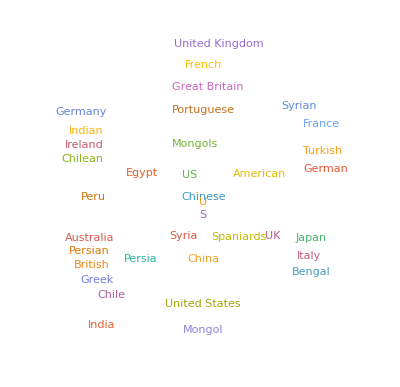

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the sea shore.","Noun"]
```

{seashells,sea,shore}

```mathematica
Length[TextCases[StringTake[WikipediaData["computers"],1000],#]]&/@{"Noun","Verb","Adjective"}
```

{54,23,20}

```mathematica
TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
Keys[TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]]
```

{Rabbit,door,voice,time,way,Mouse,moment,thing,head,table}

```mathematica
CommunityGraphPlot[First[TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]]]
```

-Graphics-

```mathematica
Length[WordList[#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{24493,6503,11392,3120}

```mathematica
Flatten[Table[WordTranslation[IntegerName[n],"French"],{n,2,10}]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

## Section 36

```mathematica
CloudPublish[Delayed[Style[RandomInteger[1000],100]]]
```

CloudObject[https://www.wolframcloud.com/obj/2859f68f-5752-4eb6-b731-2fd46e264167]

```mathematica
CloudPublish[FormFunction[{"n"->"Number"},#n^#n&]]
```

CloudObject[https://www.wolframcloud.com/obj/21e06ecb-ac76-438f-b57a-a8ee73ffa086]

```mathematica
CloudPublish[FormFunction[{"n"->"Number","n"->"Number"},#n^#p&]]
```

CloudObject[https://www.wolframcloud.com/obj/95ff140c-f08e-4fbc-89b5-d97f3e0ac2e3]

```mathematica
CloudPublish[FormFunction[{"Topic"->"String"},WordCloud[WikipediaData[#Topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/d2484caa-4bb9-4bb2-9d3b-301f1327c974]

```mathematica
CloudPublish[FormPage[{"string"->"String"},Style[StringReverse[#string],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/e0ae6743-1ba6-4d15-8aef-db6509d37e4f]

```mathematica
CloudPublish[FormPage[{"n"->"Number"},Graphics[Style[RegularPolygon[#n],RandomColor[]]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/ac45c156-0c27-4305-b54d-2f1819182ac3]

```mathematica
CloudPublish[FormPage[{"location"->"Location","n"->"Number"},GeoListPlot[GeoNearest["Volcano",#location,#n]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/63fe5f48-cb8d-4a13-8693-80a4242517c4]